Зданаие 2.2.5
-Graphics-
-Graphics-

Определим метод бисекции

```mathematica
BisecMethod[f_,A_,B_,epselon_]:=(b=B;a=A;n=0;
While[(b-a)≥2 epselon,y=(a+b)/2;
If[f[y] f[a]<0,b=y,If[f[y] f[b]<0,a=y]] n++;];
Return[{y//N,n}]);
```

Определим метод Ньютона

```mathematica
NewtoonMethod[f_,x0_,epselon_]:=(n=1;
x1=x0;
x2=x1-f[x1]/(D[f[x],x]/.x->x1);
While[Abs[x2-x1]≥epselon,{x1=x2;
x2=x1-f[x1]/(D[f[x],x]/.x->x1);
n++;}];
Return[{x2//N,n}];);
```

Данные задачи

```mathematica
ϵ=10^-6;
f[x_]:=Sqrt[x]-Cos[x];
```

Определим отрезок локализации для метода бисекции

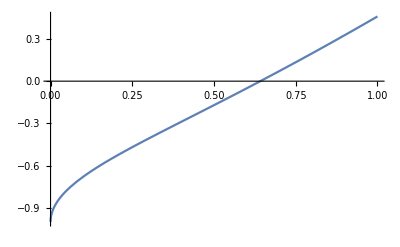

```mathematica
Plot[f[x],{x,0,1}]
```

Возьмем отрезок [0.6; 0.7]

```mathematica
A=0.6;B=0.7;
Print["Второе число - количество итераций"]
Print["Ответ методом биекции: ",BisecMethod[f,A,B,ϵ]];
Print["Ответ методом Ньютона: ",NewtoonMethod[f,(A+B)/2,ϵ]];
Print["Ответ встроенными функциями пакета:",FindRoot[f[x],{x,0}]]
```

Второе число - количество итераций

Ответ методом биекции: {0.641713,16}

Ответ методом Ньютона: {0.641714,4}

Ответ встроенными функциями пакета:{x→0.641714}